## Gaussian peaks in Fig. 2

```mathematica
Gauss[x_,μ_, width_, weight_]:=Module[{y},
σ=width/(Sqrt[2 Log[2]]);
y=weight/(σ*Sqrt[2π])Exp[-1/2((x-μ)/σ)^2]]
```

```mathematica
TripleCurve[x_]:=Gauss[x,0,0.15,0.2]+Gauss[x,1,0.8,0.4]+Gauss[x,-1,0.8,0.4]
```

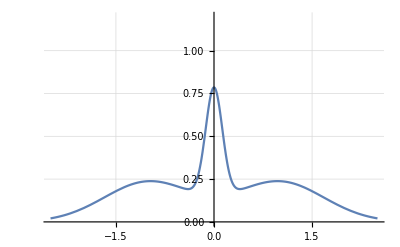

```mathematica
Plot[TripleCurve[x],{x,-2.5,2.5},PlotRange->{{-2.5,2.5},{0,1.2}},GridLines->Automatic]
```

## Transform to Imaginary time

```mathematica
G[τ_,β_]:=NIntegrate[TripleCurve[ω]Exp[-τ ω]/(1+Exp[-β ω]),{ω,-Infinity,Infinity}]
β=100.;
Ntau=1000;
```

```mathematica
TabulatedG=Table[{β/Ntau*n,G[β/Ntau*n,β]},{n,0,Ntau}];
```

```mathematica
Export[NotebookDirectory[]<>"TripleGaussianTime.dat",TabulatedG]
```

\\Client\H$\Documents\acnotes\mbook\imagb100\TripleGaussianTime.dat

## Transform to Matsubara Frequency

```mathematica
nmax=1000
```

1000

```mathematica
iωntable=Table[I(2n+1)π/β,{n,1,nmax}];
```

```mathematica
Giωntable=Table[NIntegrate[TripleCurve[ω]/(iωntable[[j]]-ω),{ω,-Infinity,Infinity}],{j,1,nmax}];
```

```mathematica
ωnReGiωntable=Table[{Im[iωntable[[j]]],Re[Giωntable[[j]]]},{j,1,nmax}];
ωnImGiωntable=Table[{Im[iωntable[[j]]],Im[Giωntable[[j]]]},{j,1,nmax}];
```

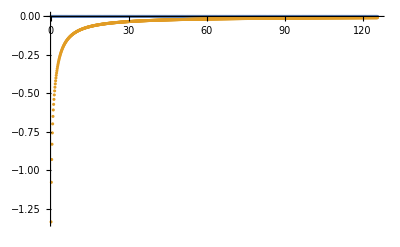

```mathematica
ListPlot[{ωnReGiωntable,ωnImGiωntable},PlotRange->All]
```

```mathematica
Export[NotebookDirectory[]<>"TripleGaussianFrequency.dat",ωnImGiωntable]
```

\\Client\C$\Users\tchen\Documents\acnotes\mbook\imaginary\TripleGaussianFrequency.dat

```mathematica
"/Users/tchen/Documents/acnotes/mbook/b50/TripleGaussianFrequency.dat"
```

/Users/tchen/Documents/acnotes/mbook/b50/TripleGaussianFrequency.dat